```mathematica
CurrentValue[$FrontEnd,"NotebookAutoSave"]=True;
```

# Dynamical Model for GRNs

```mathematica
simulatebiograph[size_]:=
Module[{incoming,outgoing,diff,index,i},
incoming= RandomChoice[Table[PDF[ExponentialDistribution[.5],#]&[i],{i,0,size*10}]->Table[i,{i,0,size*10}],size];
outgoing= Map[#-1&,RandomChoice[Table[PDF[ParetoDistribution[1.,1.2],#]&[i],{i,0,size*10}]->Table[i,{i,0,size*10}],size]];
diff = Total[incoming]-Total[outgoing];
If[diff>0,
For[i=1,i≤diff,i+=1,
index =RandomInteger[{1,Length[outgoing]}];
outgoing[[ index]]+=1;
];,
For[i=1,i≤-1*diff,i+=1,
index=RandomInteger[{1,Length[incoming]}];
incoming[[ index ]]+=1;
];
];
Return[RandomGraph[DegreeGraphDistribution[incoming,outgoing]]];
];
valuedict=<||>;
val[v2_,t2_,adj_,promoters_,inhibitors_,bpmatrix_]:=

Module[{valrec},
valrec[v_,t_]:=
Module[{presult,iresult,pused,iused,q},
If[KeyExistsQ[valuedict,{v,t}],
{v,t}/.valuedict//Return,
If[t==0,
valuedict[{v,t}]=(RandomReal[]<.5);

{v,t}/.valuedict//Return,
presult=False;
pused=False;
For[q=1,q≤Length[promoters],q+=1,
If[adj[[ promoters[[q]] ]][[  v ]]≠0 &&RandomReal[]<bpmatrix[[ promoters[[q]] ]][[v]],
pused=True;
presult = Or[presult, valrec[promoters[[q]],t-1]];
];
If[presult,Break[];];
];
iresult=False;
iused=False;
For[q=1,q≤Length[inhibitors],q+=q,
If[adj[[ inhibitors[[q]] ]][[v]]≠0 &&RandomReal[]<bpmatrix[[ inhibitors[[q]] ]][[v]],
iused=True;
iresult=Or[iresult,valrec[inhibitors[[q]],t-1]];
];
If[iresult,Break[];];
];
If[pused,
valuedict[{v,t}]=And[presult,Not[iresult]];,
valuedict[{v,t}]=valrec[v,t-1];
];
{v,t}/.valuedict//Return;
];
];
];
Return[valrec[v2,t2]];
];
```

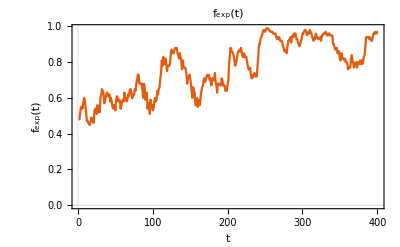

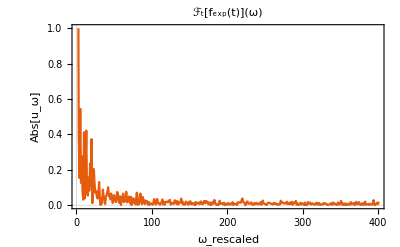

```mathematica
Size=100;
T=400;
Connectivity=.1;
Stochasticity=.9;
PromoterFraction = .5;
(*g = simulatebiograph[Size]*)
g= RandomGraph[BernoulliGraphDistribution[Size,Connectivity],DirectedEdges->True]
adj=AdjacencyMatrix[g];
MatrixPlot[adj]
promoters=RandomSample[Table[i,{i,1,Size}],Floor[Size*PromoterFraction]];
inhibitors = Complement[Table[i,{i,1,Size}],promoters];
bpmatrix=Table[Table[RandomReal[{0,1-Stochasticity}],{i,1,Size}],{j,1,Size}];
MatrixPlot[bpmatrix,PlotTheme->"Scientific"];
valuedict=<||>;
data= Monitor[Table[Table[val[v,t,adj,promoters,inhibitors,bpmatrix],{v,1,Size}],{t,0,T}],t];
Manipulate[
GraphPlot[g,Method->"CircularEmbedding",DirectedEdges->True,VertexLabeling->True,VertexRenderingFunction->({White,EdgeForm[Black],Disk[#,.05],Black,Text[data[[t+1]][[#2]],#1]}&)],{t,0,T,1}]
ListLinePlot[Table[Total[data[[t]]/.{True->1,False->0}]/Size,{t,1,T+1}],PlotRange->All,PlotTheme->"Scientific",FrameLabel->{{TraditionalForm[HoldForm[Subscript[f, exp][t]]],None},{TraditionalForm[HoldForm[t]],None}},PlotLabel->TraditionalForm[HoldForm[Subscript[f, exp][t]]],BaseStyle->{FontSize->14}]
ListLinePlot[Abs[FourierDCT[Table[Total[data[[t]]/.{True->1,False->0}]/Size,{t,1,T+1}]]],PlotRange->{{2,T},{0,1}},PlotTheme->"Scientific",FrameLabel->{{TraditionalForm[HoldForm[Abs@Subscript[u, ω]]],None},{TraditionalForm[HoldForm[Subscript[ω, rescaled]]],None}},PlotLabel->TraditionalForm[HoldForm[FourierTransform[Subscript[f, exp][t],t,ω]]],BaseStyle->{FontSize->16}]
```

```mathematica
BernoulliBioGraphExpressionSeries[Size_,T_,Connectivity_,Stochasticity_,PromoterFraction_]:=
Module[{g,adj,promoters,inhibitors,bpmatrix,data},
g= RandomGraph[BernoulliGraphDistribution[Size,Connectivity],DirectedEdges->True];
adj=AdjacencyMatrix[g];
promoters=RandomSample[Table[i,{i,1,Size}],Floor[Size*PromoterFraction]];
inhibitors = Complement[Table[i,{i,1,Size}],promoters];
bpmatrix=Table[Table[RandomReal[{0,1-Stochasticity}],{i,1,Size}],{j,1,Size}];
valuedict=<||>;
data= Table[Table[val[v,t,adj,promoters,inhibitors,bpmatrix],{v,1,Size}],{t,0,T}];
Return[data];
];
BernoulliBioGraphExpressionTotalSeries[Size_,T_,Connectivity_,Stochasticity_,PromoterFraction_]:=
Module[{g,adj,promoters,inhibitors,bpmatrix,data},
g= RandomGraph[BernoulliGraphDistribution[Size,Connectivity],DirectedEdges->True];
adj=AdjacencyMatrix[g];
promoters=RandomSample[Table[i,{i,1,Size}],Floor[Size*PromoterFraction]];
inhibitors = Complement[Table[i,{i,1,Size}],promoters];
bpmatrix=Table[Table[RandomReal[{0,1-Stochasticity}],{i,1,Size}],{j,1,Size}];
valuedict=<||>;
data= Table[Total[Table[val[v,t,adj,promoters,inhibitors,bpmatrix],{v,1,Size}]/.{True->1,False->0}],{t,0,T}];
Return[data];
];
BernoulliBioGraphExpressionTotal[Size_,T_,Connectivity_,Stochasticity_,PromoterFraction_]:=
Module[{g,adj,promoters,inhibitors,bpmatrix,data},
g= RandomGraph[BernoulliGraphDistribution[Size,Connectivity],DirectedEdges->True];
adj=AdjacencyMatrix[g];
promoters=RandomSample[Table[i,{i,1,Size}],Floor[Size*PromoterFraction]];
inhibitors = Complement[Table[i,{i,1,Size}],promoters];
bpmatrix=Table[Table[RandomReal[{0,1-Stochasticity}],{i,1,Size}],{j,1,Size}];
valuedict=<||>;
Return[Total[Table[val[v,T,adj,promoters,inhibitors,bpmatrix],{v,1,Size}]/.{True->1,False->0}]];
];
BernoulliBioGraphFirstZero[Size_,T_,Stochasticity_,PromoterFraction_]:=
Module[{Connectivity},
Connectivity=0.01;
While[Connectivity<1 && Block[{$RecursionLimit=8192},BernoulliBioGraphExpressionTotal[Size,T,Connectivity,Stochasticity,PromoterFraction]
+BernoulliBioGraphExpressionTotal[Size,T,Connectivity+.01,Stochasticity,PromoterFraction]]≠0.,
Connectivity+=.01;
];
Return[Connectivity];
];
BioGraphExpressionSeries[Size_,T_,Connectivity_,Stochasticity_,PromoterFraction_]:=
Module[{g,adj,promoters,inhibitors,bpmatrix,data},
g= RandomGraph[BernoulliGraphDistribution[Size,Connectivity],DirectedEdges->True];
adj=AdjacencyMatrix[g];
promoters=RandomSample[Table[i,{i,1,Size}],Floor[Size*PromoterFraction]];
inhibitors = Complement[Table[i,{i,1,Size}],promoters];
bpmatrix=Table[Table[RandomReal[{0,1-Stochasticity}],{i,1,Size}],{j,1,Size}];
valuedict=<||>;
data= Table[Table[val[v,t,adj,promoters,inhibitors,bpmatrix],{v,1,Size}],{t,0,T}];
Return[data];
];
BioGraphExpressionTotalSeries[Size_,T_,Connectivity_,Stochasticity_,PromoterFraction_]:=
Module[{g,adj,promoters,inhibitors,bpmatrix,data},
g= RandomGraph[BernoulliGraphDistribution[Size,Connectivity],DirectedEdges->True];
adj=AdjacencyMatrix[g];
promoters=RandomSample[Table[i,{i,1,Size}],Floor[Size*PromoterFraction]];
inhibitors = Complement[Table[i,{i,1,Size}],promoters];
bpmatrix=Table[Table[RandomReal[{0,1-Stochasticity}],{i,1,Size}],{j,1,Size}];
valuedict=<||>;
data= Table[Total[Table[val[v,t,adj,promoters,inhibitors,bpmatrix],{v,1,Size}]/.{True->1,False->0}],{t,0,T}];
Return[data];
];
BioGraphExpressionTotal[Size_,T_,Connectivity_,Stochasticity_,PromoterFraction_]:=
Module[{g,adj,promoters,inhibitors,bpmatrix,data},
g= RandomGraph[BernoulliGraphDistribution[Size,Connectivity],DirectedEdges->True];
adj=AdjacencyMatrix[g];
promoters=RandomSample[Table[i,{i,1,Size}],Floor[Size*PromoterFraction]];
inhibitors = Complement[Table[i,{i,1,Size}],promoters];
bpmatrix=Table[Table[RandomReal[{0,1-Stochasticity}],{i,1,Size}],{j,1,Size}];
valuedict=<||>;
Return[Total[Table[val[v,T,adj,promoters,inhibitors,bpmatrix],{v,1,Size}]/.{True->1,False->0}]];
];
```

```mathematica
criticalseries=ParallelTable[Print[stoch];{stoch,BernoulliBioGraphFirstZero[20,1000,stoch,.5]},{stoch,0,.9,.02}];
```

```mathematica
ListLinePlot[criticalseries,PlotTheme->"Scientific",PlotLabel->"Effect of σ on β_critical",FrameLabel->{{"β_critica",None},{"σ",None}},BaseStyle->{FontSize->16}]
```

```mathematica
finalT=600;
connseries=ParallelTable[Block[{$RecursionLimit=16484*8},Print[conn];Mean[Table[BernoulliBioGraphExpressionTotal[20,finalT,conn,0.,.5],{j,1,10}]]],{conn,.01,.8,.01}];
connseries2=ParallelTable[Block[{$RecursionLimit=16484*8},Print[conn];Mean[Table[BernoulliBioGraphExpressionTotal[20,finalT*2,conn,0.,.5],{j,1,10}]]],{conn,.01,.8,.01}];
```

```mathematica
ListLinePlot[Transpose[{Table[.01+.04*i,{i,0,Length[connseries]-1}],connseries}],PlotTheme->"Scientific",FrameLabel->{{TraditionalForm[HoldForm[⟨Subscript[f, exp][t->∞]⟩]],None},{TraditionalForm[HoldForm[Connectivity β]],None}},PlotLabel->TraditionalForm[HoldForm[Critical Collapse Value of β]],BaseStyle->{FontSize->16}]
```

```mathematica
ListLinePlot[{Transpose[{Table[.01+.04*i,{i,0,Length[connseries]-1}],connseries}],Transpose[{Table[.01+.04*i,{i,0,Length[connseries2]-1}],connseries2}]},PlotTheme->"Scientific",FrameLabel->{{TraditionalForm[HoldForm[⟨Subscript[f, exp][t->∞]⟩]],None},{TraditionalForm[HoldForm[Connectivity β]],None}},PlotLabel->TraditionalForm[HoldForm[Critical Collapse Value of β]],BaseStyle->{FontSize->16},
PlotLegends->Placed[LineLegend@{"T_final=600","T_Final=1200"},{.75,.75}]]
```

```mathematica
fourierconnseries=ParallelMap[{#[[1]],Abs[FourierDCT[#[[2]]]]}&,DeleteCases[ParallelTable[Block[{$RecursionLimit=4096},Print[conn];{conn,BernoulliBioGraphExpressionTotalSeries[100,90,conn,0.,.5]}],{conn,.01,.9,.02}],l_/;l[[2]][[-1]]==0]];
```

```mathematica
Manipulate[ListLinePlot[fourierconnseries[[i]][[2]][[3;;]],PlotLabel->TraditionalForm["β = "~StringJoin~ToString@fourierconnseries[[i]][[1]] ],PlotTheme->"Scientific",PlotRange->{0,Max[fourierconnseries[[i]][[2]][[3;;]]]}],{i,1,Length[fourierconnseries],1}]
```

```mathematica
ListLinePlot[Transpose[{Table[fourierconnseries[[j]][[1]],{j,1,Length[fourierconnseries],1}],Table[Total[Table[j*fourierconnseries[[i]][[2]][[j]],{j,3,Length[fourierconnseries[[i]][[2]]]}]]/(Total[fourierconnseries[[i]][[2]]]),{i,1,Length[fourierconnseries]}]}],PlotTheme->"Scientific",FrameLabel->{{TraditionalForm[HoldForm[Sum[Subscript[ω, i]*Subscript[u, Subscript[ω, i]],{i,0,N}]/Sum[Subscript[u, Subscript[ω, i]],{i,0,N}]]],None},{TraditionalForm[HoldForm[Connnectivity β]],None}},PlotLabel->TraditionalForm[HoldForm[Flow of Information from Low Frequency to High as β->1]],BaseStyle->{FontSize->16}]
```

```mathematica
fourierstochseries= ParallelMap[{#[[1]],Abs[FourierDCT[#[[2]]]]}&,DeleteCases[ParallelTable[Block[{$RecursionLimit=4096},Print[stoch];{stoch,BernoulliBioGraphExpressionTotalSeries[100,90,.8,stoch,.5]}],{stoch,0,.9,.02}],l_/;l[[2]][[-1]]==0]];
```

0.

0.12

0.24

0.36

0.26

0.38

0.14

0.28

0.16

0.4

0.02

0.3

0.42

0.18

0.44

0.2

0.32

0.46

0.22

0.34

0.04

0.48

0.6

0.72

0.5

0.62

0.74

0.06

0.52

0.64

0.76

0.54

0.66

0.08

0.78

0.56

0.68

0.1

0.58

0.8

0.7

0.82

0.84

0.86

0.88

0.9

```mathematica
Manipulate[ListLinePlot[fourierstochseries[[i]][[2]][[3;;]],PlotLabel->TraditionalForm["σ = "~StringJoin~ToString@(1-fourierstochseries[[i]][[1]] )],PlotTheme->"Scientific",PlotRange->{0,Max[fourierstochseries[[i]][[2]][[3;;]]]}],{i,1,Length[fourierstochseries],1}]
```

```mathematica
ListLinePlot[Transpose[{Table[fourierstochseries[[j]][[1]],{j,1,Length[fourierstochseries],1}],Table[Total[Table[j*fourierstochseries[[i]][[2]][[j]],{j,3,Length[fourierstochseries[[i]][[2]]]}]]/(Total[fourierstochseries[[i]][[2]]]),{i,1,Length[fourierstochseries]}]}],PlotTheme->"Scientific",FrameLabel->{{TraditionalForm[HoldForm[Sum[Subscript[ω, i]*Subscript[u, Subscript[ω, i]],{i,0,N}]/Sum[Subscript[u, Subscript[ω, i]],{i,0,N}]]],None},{TraditionalForm[HoldForm[BP bound σ]],None}},PlotLabel->TraditionalForm[HoldForm[Flow of Information from High Frequency to Low as σ->0 (β=.8)]],BaseStyle->{FontSize->16}]
```